```mathematica
(*(ccdata[7]/.{x_,y_}/;x>maxyx->{x,0})[[All,2]]*)
```

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

## Define Functions

```mathematica
BW[w_,wr_,Γ_,δbg_,const_,shift_,shift2_]:=
const((Γ/2)^2/((w-wr)^2+(Γ/2)^2))+ δbg((Γ/2)(w-wr))/((w-wr)^2+(Γ/2)^2)+0 ((4 (w-wr)^2- Γ^2) deltabg^2)/(4 (w-wr)^2+Γ^2)+shift (w-wr)+shift2 ;
BWi[w_,wr_,Γ_,const_]:=const((Γ/2)^2/((w-wr)^2+(Γ/2)^2)) ;

fitnew[input_,output_,Tscan_]:=Module[{temp=Range[1,Length[Tscan]],n,maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,inputc,bad},
SetSharedVariable[temp];
ParallelDo[n=temp[[ii]];
maxx=Max[input[n][[All,1]]];
minx=Min[input[n][[All,1]]];
maxy=Max[input[n][[All,2]]];
maxyx=input[n][[Position[input[n],Max[input[n][[All,2]]]][[1,1]],1]];
maxyi=Position[input[n][[All,1]],maxyx][[1,1]];
maxxy=input[n][[Position[input[n],Max[input[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[input[n],InterpolationOrder->1];maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],maxyx≤x≤maxx},{x,a}],maxxy],FindArgMax[{inter[x],maxyx≤x≤maxx},{x,a}][[1]]},{a,maxyx,maxx,(maxx-maxyx)/50}],First][[All,2]]]];
bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[n][[All,1]],Nearest[input[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[n][[maxxis[[i]]-30,2]]>input[n][[maxxis[[i]],2]],input[n][[maxxis[[i]]+30,2]]>input[n][[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input[n]],maxyi+3(maxyi-hwhmi),Length[input[n]]]};];
If[mins[[1]]<0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[n][[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[n][[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];
temp[[ii]]=Range[Length[hwhmi]];
Do[temp[[ii,i]]=NonlinearModelFit[inputc[[i]],{BW[w,wr,Γ,δbg,const,shift,shift2],const>0,Γ>0},{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w,MaxIterations->1000],{i,Length[hwhmi]}];Print[ii];,{ii,Length[Tscan]}];output=temp;];

store[param_,res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=param/.model[[i,ii]]["BestFitParameters"],{ii,Length[res[[i]]]}],{i,Length[res]}];Export["spectraldata/Tscan/results/newK/"<>temp<>".dat",res];];

storearea[res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=π/2(Γ/.model[[i,ii]]["BestFitParameters"])( const/.model[[i,ii]]["BestFitParameters"]),{ii,Length[res[[i]]]}],{i,Length[res]}];Export["spectraldata/Tscan/results/newK/"<>temp<>".dat",res];];

import[res_]:=res=Import["spectraldata/Tscan/results/newK/"<>ToString[res]<>".dat"];
```

## Charmonium

### Import Data

```mathematica
Tscanc={155,180,200};
```

```mathematica
Do[ccdata[n]=Import["spectraldata/Tscan/cc/newK/swccT"<>ToString[Tscanc[[n]]]<>"spectra.dat"];,{n,Length[Tscanc]}];
Manipulate[ListPlot[ccdata[n],Joined->True],{n,1,Length[Tscanc],1}]
```

```mathematica
Do[ccdatau[n]=Import["spectraldata/Tscan/cc/newK/swccT"<>ToString[Tscanc[[n]]]<>"uspectra.dat"];,{n,Length[Tscanc]}];
Manipulate[ListPlot[ccdatau[n],Joined->True],{n,1,Length[Tscanc],1}]
```

```mathematica
Do[ccdatal[n]=Import["spectraldata/Tscan/cc/newK/swccT"<>ToString[Tscanc[[n]]]<>"lspectra.dat"];,{n,Length[Tscanc]}];
Manipulate[ListPlot[ccdatal[n],Joined->True],{n,1,Length[Tscanc],1}]
```

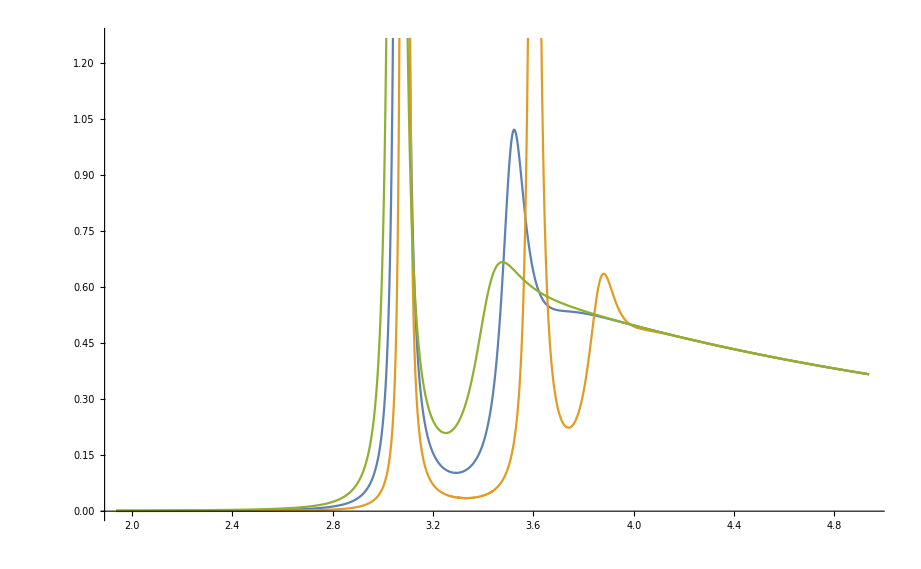

```mathematica
ListPlot[{ccdata[1],ccdatal[1],ccdatau[1]},Joined->True]
```

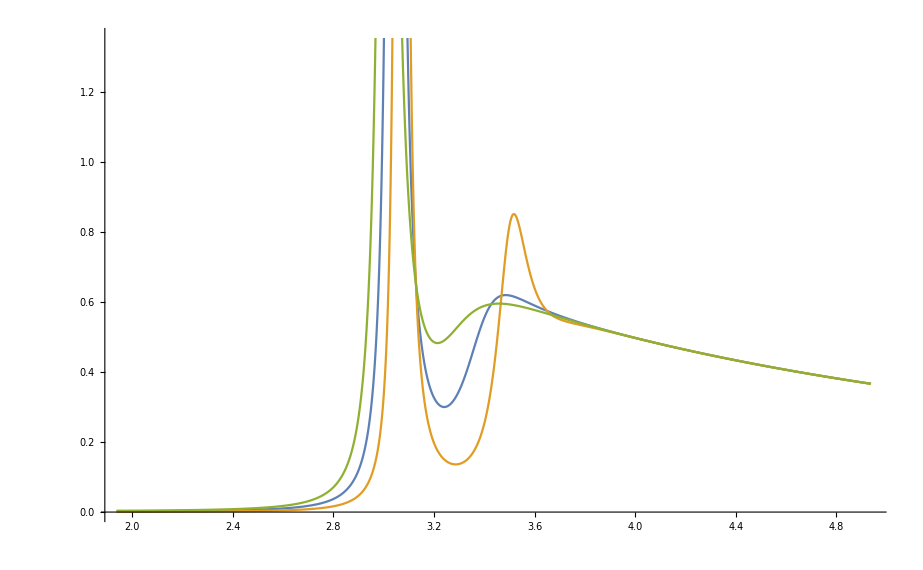

```mathematica
ListPlot[{ccdata[2],ccdatal[2],ccdatau[2]},Joined->True]
```

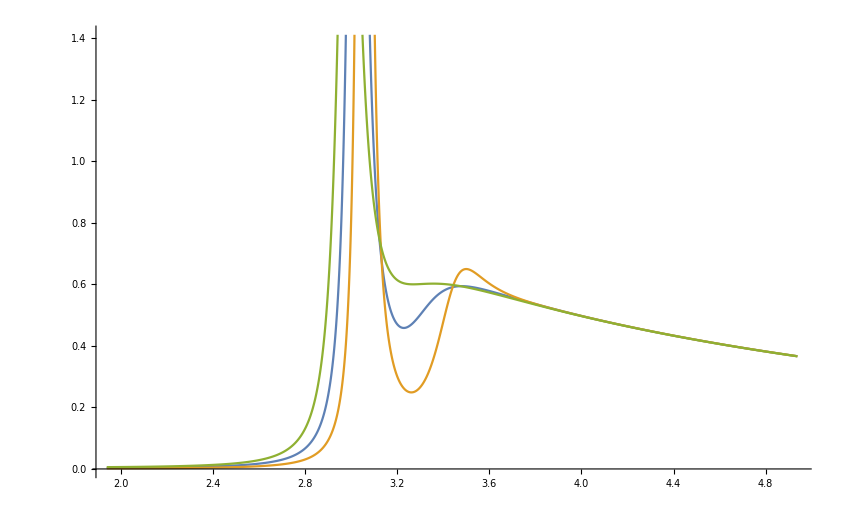

```mathematica
ListPlot[{ccdata[3],ccdatal[3],ccdatau[3]},Joined->True]
```

### Fitting

```mathematica
Clear[ccmodelu,ccmodell,ccmodel]
fitnew[ccdata,ccmodel,Tscanc];
fitnew[ccdatal,ccmodell,Tscanc];
fitnew[ccdatau,ccmodelu,Tscanc];
```

3

2

1

3

2

1

2

3

1

### Store Results

```mathematica
Do[If[Length[ccmodel[[i]]]>2,ccmodel[[i]]=ccmodel[[i,;;2]]];If[Length[ccmodelu[[i]]]>2,ccmodelu[[i]]=ccmodelu[[i,;;2]]];If[Length[ccmodell[[i]]]>2,ccmodell[[i]]=ccmodell[[i,;;2]]];,{i,Length[ccmodel]}];
```

```mathematica
Clear[wrfitcc,wrfitccl,wrfitccu,gfitcc,gfitccl,gfitccu,areafitcc,areafitccu,areafitccl,cfitcc,cfitccl,cfitccu,dfitcc,dfitccl,dfitccu,sfitcc,sfitccl,sfitccu,s2fitcc,s2fitccl,s2fitccu];
store[wr,wrfitcc,ccmodel];
store[wr,wrfitccl,ccmodell];
store[wr,wrfitccu,ccmodelu];
store[Γ,gfitcc,ccmodel];
store[Γ,gfitccl,ccmodell];
store[Γ,gfitccu,ccmodelu];
store[const,cfitcc,ccmodel];
store[const,cfitccl,ccmodell];
store[const,cfitccu,ccmodelu];
store[δbg,dfitcc,ccmodel];
store[δbg,dfitccl,ccmodell];
store[δbg,dfitccu,ccmodelu];
store[shift,sfitcc,ccmodel];
store[shift,sfitccl,ccmodell];
store[shift,sfitccu,ccmodelu];
store[shift2,s2fitcc,ccmodel];
store[shift2,s2fitccl,ccmodell];
store[shift2,s2fitccu,ccmodelu];
storearea[areafitcc,ccmodel];
storearea[areafitccl,ccmodell];
storearea[areafitccu,ccmodelu];
```

### Display Results

```mathematica
Do[If[Length[wrfitcc[[-i]]]<2,cc1Tcut=Length[wrfitcc]-i];,{i,Length[wrfitcc]}];
Do[If[Length[wrfitccu[[-i]]]<2,cc1uTcut=Length[wrfitccu]-i];,{i,Length[wrfitccl]}];
Do[If[Length[wrfitccl[[-i]]]<2,cc1lTcut=Length[wrfitccl]-i];,{i,Length[wrfitccu]}];
```

```mathematica
Manipulate[Show[{ListPlot[ccdata[i],Joined->True,PlotRange->All],Plot[BW[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],dfitcc[[i,ii]],cfitcc[[i,ii]],sfitcc[[i,ii]],s2fitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],cfitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[wrfitcc],1},{ii,1,Length[wrfitcc[[1]]],1}]
```

```mathematica
Manipulate[Show[{ListPlot[ccdatau[i],Joined->True],Plot[BW[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],dfitccu[[i,ii]],cfitccu[[i,ii]],sfitccu[[i,ii]],s2fitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],cfitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[wrfitccu],1},{ii,1,Length[wrfitccu[[1]]],1}]
```

```mathematica
Manipulate[Show[{ListPlot[ccdatal[i],Joined->True,PlotRange->All],Plot[BW[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],dfitccl[[i,ii]],cfitccl[[i,ii]],sfitccl[[i,ii]],s2fitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],cfitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[wrfitccl],1},{ii,1,Length[wrfitccl[[1]]],1}]
```

## Dilepton Emission Rates

```mathematica
Emfactor=2.356305815440891;
nB[w_,T_]:=1/(Exp[w/T]-1);
```

```mathematica
R0=ConstantArray[0,3];
Do[R0[[ii]]={Tscanc[[ii]],Emfactor (areafitcc[[ii,2]]nB[wrfitcc[[ii,2]],Tscanc[[ii]]/1000])/(areafitcc[[ii,1]]nB[wrfitcc[[ii,1]],Tscanc[[ii]]/1000])},{ii,3}];
R0l=ConstantArray[0,3];
Do[R0l[[ii]]={Tscanc[[ii]],Emfactor (areafitccl[[ii,2]]nB[wrfitccl[[ii,2]],Tscanc[[ii]]/1000])/(areafitccl[[ii,1]]nB[wrfitccl[[ii,1]],Tscanc[[ii]]/1000])},{ii,3}];
R0u=ConstantArray[0,3];
Do[R0u[[ii]]={Tscanc[[ii]],Emfactor (areafitccu[[ii,2]]nB[wrfitccu[[ii,2]],Tscanc[[ii]]/1000])/(areafitccu[[ii,1]]nB[wrfitccu[[ii,1]],Tscanc[[ii]]/1000])},{ii,3}];
```

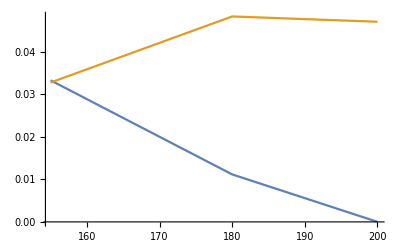

```mathematica
ListLinePlot[{R0,R0l}]
```

```mathematica
R0
```

{{155,0.0332438},{180,0.0111523},{200,9.71072×10^-6}}

```mathematica
R0l
```

{{155,0.0327234},{180,0.0482379},{200,0.0469979}}

```mathematica
R0u
```

{{155,0.0298952},{180,0.0000131979},{200,0.00452843}}

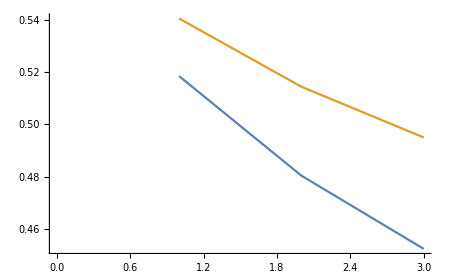

```mathematica
ListLinePlot[{areafitcc[[All,1]],areafitccl[[All,1]]}]
```

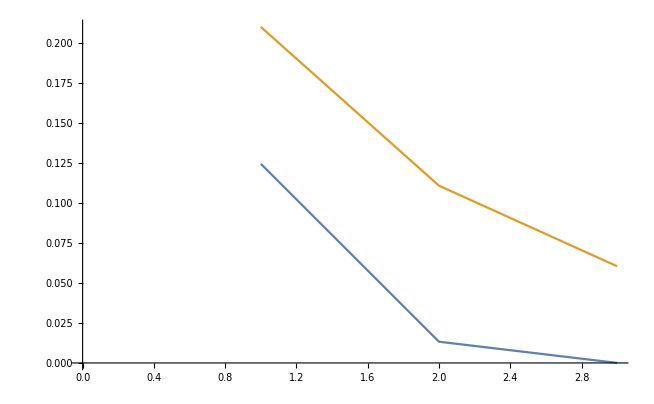

```mathematica
ListLinePlot[{areafitcc[[All,2]],areafitccl[[All,2]]}]
```

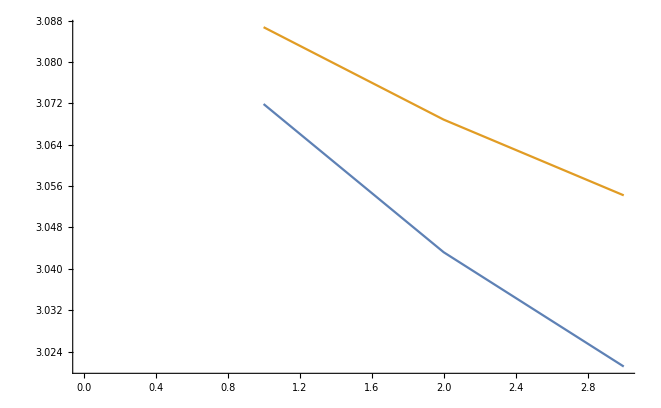

```mathematica
ListLinePlot[{wrfitcc[[All,1]],wrfitccl[[All,1]]}]
```

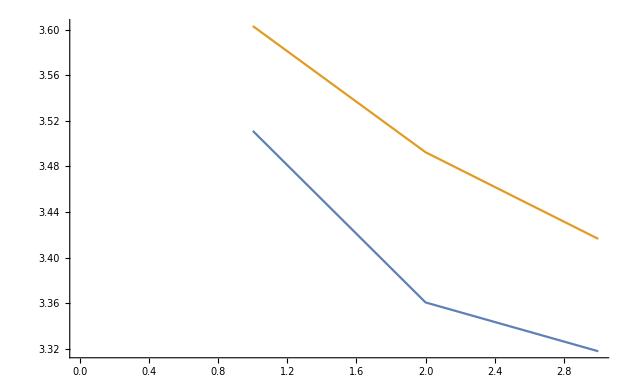

```mathematica
ListLinePlot[{wrfitcc[[All,2]],wrfitccl[[All,2]]}]
```

```mathematica
Emfactor (areafitccl[[1,2]]nB[wrfitccl[[1,2]],Tscanc[[1]]/1000])/(areafitccl[[1,1]]nB[wrfitccl[[1,1]],Tscanc[[1]]/1000])
```

0.0327234

```mathematica
Emfactor (areafitcc[[1,2]]nB[wrfitcc[[1,2]],Tscanc[[1]]/1000])/(areafitcc[[1,1]]nB[wrfitcc[[1,1]],Tscanc[[1]]/1000])
```

0.0332438